## Subroutines, run this first

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
showCurveMain[pts_,width_]:= Graphics3D[{Blue,Specularity[0.3],CapForm[None],Tube[pts,width]}]
```

```mathematica
importData[noRods_,nseg_,len_,F_,Fs_,K3_,bsrat_,outerBC_,bcs_,typeInd_]:= Block[{angOut,stPos,FileGot,lowestOut},
If[FileExistsQ[StringJoin["lamina_NROD",ToString[noRods],"_NSEG_",ToString[nseg],"_RAT",ToString[len],"/",numToThree[F],"F_S",numToFour[Fs],"K3",ToString[K3],"BsRat",numToTwo[bsrat],"Obc",numToDot[outerBC],"_",ToString[typeInd],"/lowest" ]]==True,
angOut=Drop[Import[StringJoin["lamina_NROD",ToString[noRods],"_NSEG_",ToString[nseg],"_RAT",ToString[len],"/",numToThree[F],"F_S",numToFour[Fs],"K3",ToString[K3],"BsRat",numToDot[bsrat],"Obc",numToDot[outerBC],"_",ToString[typeInd],"/lowest" ] ,"List"],4];
stPos =Import[StringJoin["lamina_NROD",ToString[noRods],"_NSEG_",ToString[nseg],"_RAT",ToString[len],"/",numToThree[F],"F_S",numToFour[Fs],"K3",ToString[K3],"BsRat",numToTwo[bsrat],"Obc",numToDot[outerBC],"_",ToString[typeInd],"/initpos" ] ,"Table"];
lowestOut =StringCases[Import[StringJoin["lamina_NROD",ToString[noRods],"_NSEG_",ToString[nseg],"_RAT",ToString[len],"/",numToThree[F],"F_S",numToFour[Fs],"K3",ToString[K3],"BsRat",numToTwo[bsrat],"Obc",numToDot[outerBC],"_",ToString[typeInd],"/lowest" ] ,"List"][[3]],x:NumberString:>ToExpression[x]];
FileGot = True;
,
FileGot = False;
];
If[FileGot ==False,
{0,0},
{stPos,angOut,lowestOut[[1]]*(10^lowestOut[[2]])}
]
];
```

```mathematica
findMinimumSet[noRods_,nseg_,len_,F_,Fs_,K3_,bsrat_,outerBC_,bcs_]:= Block[{energySet,enMin,minpositions},
energySet={importData[noRods,nseg,len,F,Fs,K3,bsrat,outerBC,bcs,1][[3]],importData[noRods,nseg,len,F,Fs,K3,bsrat,outerBC,bcs,2][[3]],importData[noRods,nseg,len,F,Fs,K3,bsrat,outerBC,bcs,3][[3]],importData[noRods,nseg,len,F,Fs,K3,bsrat,outerBC,bcs,4][[3]]};
Print["energy set"];
Print[energySet];
energySet = energySet/Min[energySet];
enMin = Min[energySet];
minpositions =Flatten[Position[energySet,_?(Abs[#-enMin]<0.001&)]];
If[Length[minpositions]==1,
classifyConfigAngKap[noRods,nseg,len,F,Fs,K3,bsrat,outerBC,bcs,minpositions[[1]]]
,
(*check if types are genuinelu different*)
Union[Table[classifyConfigAngKap[noRods,nseg,len,F,Fs,K3,bsrat,outerBC,bcs,minpositions[[i]]],{i,1,Length[minpositions]}]]
]
];
```

```mathematica
makeCoords[datIn_,lenRod_,noCoords_,noRods_,col_]:= Block[{coords,dat,stpts},
dat=datIn[[2]];
stpts=datIn[[1]];
coords= Table[Accumulate[Table[{(lenRod/noCoords) Cos[dat[[(j-1)*(noCoords-1)+i]]],0,(lenRod/noCoords)Sin[dat[[(j-1)*(noCoords-1)+i]]]},{i,1,noCoords-1}]],{j,1,noRods}];
coords=Table[Table[coords[[j,i]]+{stpts[[j,1]],0,stpts[[j,2]]},{i,1,Length[coords[[j]]]}],{j,1,noRods}];
Show[Table[Graphics3D[{col,Specularity[0.4],Tube[coords[[i]],Abs[stpts[[2,2]]-stpts[[1,2]]]/5]}],{i,1,noRods}],ImageSize->Large,ViewPoint->Front,Boxed->False,PlotRangePadding->0,ImagePadding->0]
];
```

```mathematica
getCoords[datIn_,lenRod_,noCoords_,noRods_]:= Block[{coords,dat,stpts},
dat=datIn[[2]];
stpts=datIn[[1]];
coords= Table[Accumulate[Table[{(lenRod/noCoords) Cos[dat[[(j-1)*(noCoords-1)+i]]],0,(lenRod/noCoords)Sin[dat[[(j-1)*(noCoords-1)+i]]]},{i,1,noCoords-1}]],{j,1,noRods}];
coords=Table[Table[coords[[j,i]]+{stpts[[j,1]],0,stpts[[j,2]]},{i,1,Length[coords[[j]]]}],{j,1,noRods}];
coords
];
```

```mathematica
numToTwo[number_]:= Block[{origCast,strout},
origCast=ToString[number];
If[number≥ 1.0,
If[StringLength[origCast]≥1,
strout=StringJoin[origCast,"0"];
,
strout=origCast;
];
,
strout=origCast;
];
strout
];
```

```mathematica
numToDot[number_]:= Block[{origCast,strout},
origCast=ToString[number];
If[number≥ 1.0,
If[Last[Characters[origCast]]==".",
strout=StringJoin[origCast,"0"];
,
strout=origCast;
];
,
strout=origCast;
];
strout
];
```

```mathematica
numToThree[number_]:= Block[{origCast,strout},
origCast=ToString[number];
If[StringLength[origCast]==3,
strout=StringJoin[origCast,"00"];
];
If[StringLength[origCast]==4,
strout=StringJoin[origCast,"0"];
];
If[StringLength[origCast]==2,
strout=StringJoin[origCast,"000"];
];
If[StringLength[origCast]==5,
strout=origCast;
];
strout
];
```

```mathematica
numToFour[number_]:= Block[{origCast,strout},
origCast=ToString[number];
If[StringLength[origCast]==3,
strout=StringJoin[origCast,"000"];
];
If[StringLength[origCast]==4,
strout=StringJoin[origCast,"00"];
];
If[StringLength[origCast]==5,
strout=StringJoin[origCast,"0"];
];
If[StringLength[origCast]==2,
strout=StringJoin[origCast,"0000"];
];
If[StringLength[origCast]>5,
strout=origCast
];
strout
];
```

```mathematica
getConfig[noRods_,nseg_,len_,F_,Fs_,K3_,bsrat_,outerBC_,col_,bcs_,typeInd_]:=Block[{dat},
dat=importData[noRods,nseg,len,F,Fs,K3,bsrat,outerBC,bcs,typeInd];
(*makeCoords[dat,len,nseg,noRods,col]*)
If[Length[dat[[1]]]==0,
Print["file not there brah"];
,
makeCoords[dat,len,nseg,noRods,col]
]
];
```

```mathematica
writeConfig[noRods_,nseg_,len_,F_,Fs_,K3_,bsrat_,outerBC_,col_,bcs_,typeInd_]:=Block[{dat,plt,str},
dat=importData[noRods,nseg,len,F,Fs,K3,bsrat,outerBC,bcs,typeInd];
plt = makeCoords[dat,len,nseg,noRods,col];
If[bcs=="clamped",
str=StringJoin["lamina_NROD",ToString[noRods],"_NSEG",ToString[nseg],"_RAT",ToString[len],"_Clamped\\",numToThree[F],"F_S",numToFour[Fs],"K3",ToString[K3],"BsRat",ToString[bsrat],"0Obc",ToString[outerBC],"\\config.png"];
,
str=StringJoin["lamina_NROD",ToString[noRods],"_NSEG",ToString[nseg],"_RAT",ToString[len],"\\",numToThree[F],"F_S",numToFour[Fs],"K3",ToString[K3],"BsRat",ToString[bsrat],"0Obc",ToString[outerBC],"\\config.png"];
];
Export[str,plt];
Delete[plt];
];
```

```mathematica
evaluateShape[datIn_,lenRod_,noCoords_,noRods_]:= Block[{coords,dat,stpts,angs,kapSet,meanCurvatures,meanAngles,MeanDeflec,unweightedmean,weightedmean,MeanAbsDeflec,MeanDeflec1,MeanDeflec2,MeanDeflec3,MeanDeflec4,MeanDeflec5,MeanAbsDeflec1,MeanAbsDeflec2,MeanAbsDeflec3,MeanAbsDeflec4,pinchRatio ,MeanAbsDeflec5,ind1,ind2,mid,MeanAbsDeflecMid},
dat=datIn[[2]];
angs =Transpose[Table[dat[[(j-1)*(noCoords-1)+i]],{i,1,noCoords-1},{j,1,noRods}]];
kapSet =Table[Table[Tan[angs[[j,i+1]]-angs[[j,i]]]^2,{i,1,Length[angs[[j]]]-1}],{j,1,noRods}];
meanCurvatures = Map[Mean,kapSet];
unweightedmean =Mean[meanCurvatures];
coords =getCoords[datIn,lenRod,noCoords,noRods];
If[EvenQ[noRods]==True,
mid= noRods/2;
,
mid= Round[noRods+1/2];
];
MeanAbsDeflec=Table[Mean[Table[Abs[coords[[i,Floor[j*noCoords/11],3]]-datIn[[1,i,2]]]/(1/(noRods-1)),{i,1,noRods}]],{j,1,10}];
MeanAbsDeflecMid=Mean[Table[Mean[Table[Abs[coords[[i,Floor[j*noCoords/11],3]]-datIn[[1,i,2]]]/(1/(noRods-1)),{i,mid,mid}]],{j,1,10}]];
ind1=Floor[(noRods+1)/2];
ind2=Ceiling[(noRods+1)/2];
MeanDeflec=Table[Mean[Table[(coords[[i,Floor[j*noCoords/11],3]]-datIn[[1,i,2]])/(1/(noRods-1)),{i,1,noRods}]],{j,1,10}];
(*Outer inner pinch*)
pinchRatio = Abs[coords[[1,Floor[noCoords/2],3]]-coords[[noRods,Floor[noCoords/2],3]]]/Abs[coords[[1,1,3]]-coords[[noRods,1,3]]];

{Abs[Mean[MeanDeflec]],Mean[MeanAbsDeflec],pinchRatio,MeanAbsDeflecMid}
];
```

```mathematica
getAngKappa[noRods_,nseg_,len_,F_,Fs_,K3_,bsrat_,outerBC_,bcs_,typeInd_]:= Block[{coords,dat,stpts,angs,kapSet,meanCurvatures,meanAngles,MeanDeflec,unweightedmean,weightedmean,MeanAbsDeflec,MeanDeflec1,MeanDeflec2,MeanDeflec3,MeanDeflec4,MeanDeflec5,MeanAbsDeflec1,MeanAbsDeflec2,MeanAbsDeflec3,MeanAbsDeflec4,pinchRatio ,MeanAbsDeflec5,ind1,ind2,mid,MeanAbsDeflecMid,noCoords},
noCoords=nseg;
dat= importData[noRods,nseg,len,F,Fs,K3,bsrat,outerBC,bcs,typeInd][[2]];
angs =Transpose[Table[dat[[(j-1)*(noCoords-1)+i]],{i,1,noCoords-1},{j,1,noRods}]];
kapSet =Table[Table[Tan[0.5(angs[[j,i+1]]-angs[[j,i]])]^2/(len/(noCoords-1)),{i,1,Length[angs[[j]]]-1}],{j,1,noRods}];
{angs,outerBC*kapSet}
];
```

```mathematica
classifyConfig[noRods_,nseg_,len_,F_,Fs_,K3_,bsrat_,outerBC_,bcs_,typeInd_]:=Block[{dat,shapePars},
dat = importData[noRods,nseg,len,F,Fs,K3,bsrat,outerBC,bcs,typeInd];
shapePars =evaluateShape[dat,len,nseg,noRods];
(*Print[shapePars];*)
(*0 = essentialy underformed, 1= full buckled 2 =internally buckeld 3 = auxetic pinch *)
If[shapePars[[2]]>noRods/4.0,
1,
If[shapePars[[2]]>0.1,
(*reasonable curveature*)
If[shapePars[[1]]<0.0001 ||shapePars[[3]]<0.5 ||shapePars[[4]]<0.2,
3,
2
]
,
If[shapePars[[2]]>noRods/50.0,
3
,
0
]
]
]
];
```

```mathematica
outBCNo[intIn_]:= Which[intIn==1,0.01,intIn==2,0.05,intIn==3,0.22,intIn==4,1.0,intIn==5,4.0,intIn==6,20.0,intIn==7,100.0];
```

```mathematica
sphereIndicator[type_,pos_,rad_]:= Block[{col},
If[type==0,
col= Black;
,
If[type==1,
col =  Yellow
,
If[type==2,
col = Blue
,
col= Red;
];
];
];
Graphics3D[{col,Opacity[1.0],Specularity[0.3],Ellipsoid[N[{pos[[1]],pos[[2]],pos[[3]]}],{(0.1-0.005)/9/rad,(0.004-0.0005)/8/rad,5/5/rad/2}]}]
];
```

```mathematica
classifyConfigAngKap[noRods_,nseg_,len_,F_,Fs_,K3_,bsrat_,outerBC_,bcs_,typeInd_]:=Block[{dat,shapePars,meanAbsMoment,meantotalinternalmoment,meantotalexternalmoment,midPoint,angSet,symparam},
shapePars =getAngKappa[noRods,nseg,len,F,Fs,K3,bsrat,outerBC,bcs,typeInd];
(*Print[shapePars];*)
(*0 = essentialy underformed, 1= full buckled 2 =internally buckeld 3 = auxetic pinch *)
meanAbsMoment= Mean[Map[Mean,Abs[shapePars[[2]]]]];
meantotalinternalmoment =Mean[Map[Mean,Abs[shapePars[[2]][[2;;Length[shapePars[[2]]]-1]]]]];
meantotalexternalmoment =Mean[{Mean[Abs[shapePars[[2]][[1]]]],Mean[Abs[Last[shapePars[[2]]]]]}];
(*symmetry parameter*)
angSet = shapePars[[1]];
If[EvenQ[noRods]==True,
midPoint = Round[(noRods+1)/2];
symparam=Mean[Table[Mean[Table[Abs[angSet[[noRods-i,j]]+angSet[[i,j]]],{j,1,Length[angSet[[1]]]}]],{i,1,midPoint}]];
,
midPoint =Round[noRods/2];
symparam=Mean[Table[Mean[Table[Abs[angSet[[noRods-i,j]]+angSet[[i,j]]],{j,1,Length[angSet[[1]]]}]],{i,1,midPoint}]];
];
(*Print[meanAbsMoment," ",meantotalinternalmoment/meantotalexternalmoment, " ",symparam];*)
If[meanAbsMoment<0.0000000001,
0,
If[meantotalinternalmoment/meantotalexternalmoment >5,
2
,
If[symparam>0.1,
1
,
3
]
]
]
];
```

```mathematica
nrods=10;nseg=200;length=5;Nc=0.15;Ns=0.0;k3=0.0002;BsRat=1.0;Br=100.0;
```

```mathematica
nrods=10;
```

```mathematica
k3=0.0002;
```

```mathematica
{findMinimumSet[nrods,nseg,length,0.1,0.0,k3,BsRat,Br,"clamped"],Table[getConfig[nrods,nseg,length,0.1,0.0,k3,
BsRat,Br ,Blue,"clamped",j],{j,1,4}]}
```

energy set

{5000.,5000.,5000.,5000.}

{{2},{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}}

```mathematica
{findMinimumSet[nrods,nseg,length,0.105,0.0,k3,BsRat,Br,"clamped"],Table[getConfig[nrods,nseg,length,0.105,0.0,k3,
BsRat,Br ,Blue,"clamped",j],{j,1,4}]}
```

energy set

{5250.,5250.,5250.,5250.16}

{{2},{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}}

```mathematica
{findMinimumSet[nrods,nseg,length,0.11,0.0,k3,BsRat,Br,"clamped"],Table[getConfig[nrods,nseg,length,0.11,0.0,k3,
BsRat,Br ,Blue,"clamped",j],{j,1,4}]}
```

energy set

{5494.45,5494.34,5494.34,5494.45}

{{2},{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}}

```mathematica
0.11/0.01
```

11.

```mathematica
N[Table[n^2Pi^2/25,{n,1,6}]]
```

{0.394784,1.57914,3.55306,6.31655,9.8696,14.2122}

```mathematica
kapt201= getAngKappa[nrods,nseg,length,0.105,0.0,k3,BsRat,100.0,"clamped",4];
```

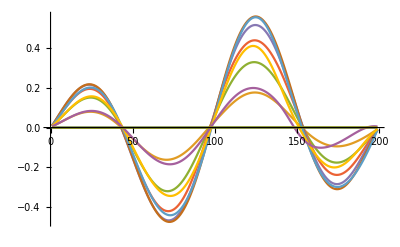

```mathematica
ListPlot[Table[kapt201[[1,j]],{j,1,Length[kapt201[[1]]]}],Joined-> True]
```

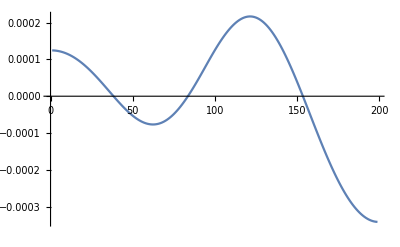
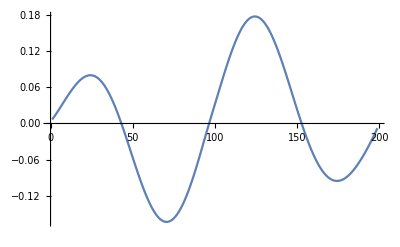
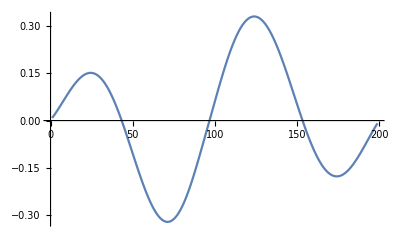
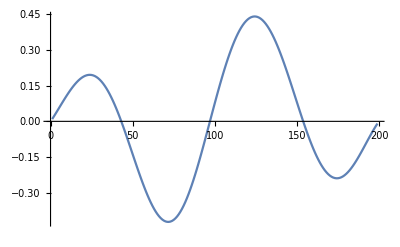
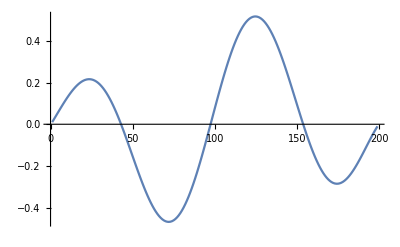
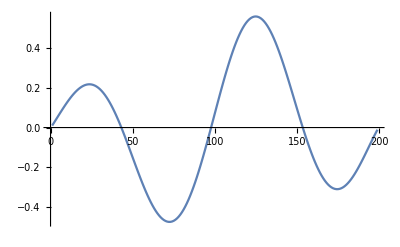
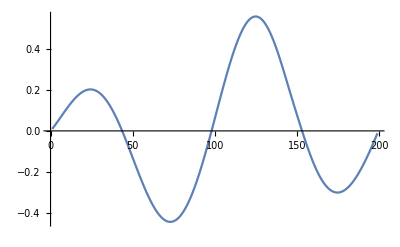
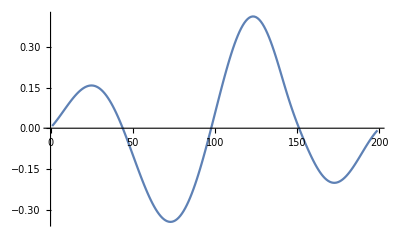

```mathematica
Table[ListPlot[kapt201[[1,j]],Joined-> True],{j,1,Length[kapt201[[2]]]}]
```

```mathematica
Clear[Nc];
```

```mathematica
lSol[s_,n_,L_,A2_]:= A2 (Cos[2 n/L π s] -1);
```

```mathematica
D[lSol[s,n,L,A2],s]
```

```mathematica
Sqrt[(2 A2 n π Sin[(2 n π s)/L])/L(2 A2 n π Sin[(2 n π s)/L])/L]
```

```mathematica
ldSol[s_,n_,L_,A2_]:=2 π (A2 n Sin[(2 n π s)/L]^2)/L;
```

```mathematica
Plot[ldSol[]
```

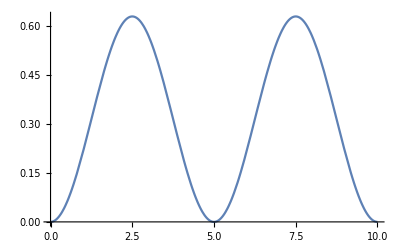

```mathematica
Plot[ldSol[s,1,10,1],{s,0,10}]
```

```mathematica
lSolWeighted[s_,n_,L_]:= -(2 n π)/(2 n π-Sin[2 n π]) (Cos[2 n/L π s] -1);
```

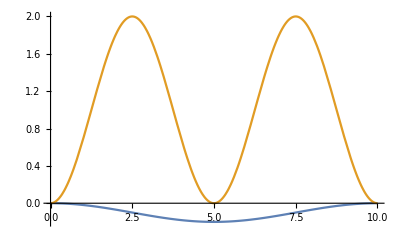

```mathematica
Plot[{lSol[s,1,10,0.1],lSolWeighted[s,2,10]},{s,0,10}]
```

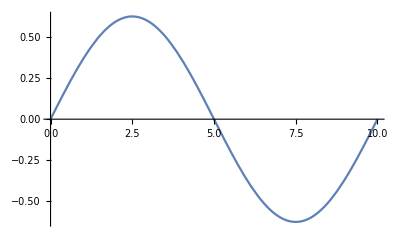

```mathematica
Plot[D[lSol[ss,1,10,-1],ss]/.{ss->s},{s,0,10}]
```

```mathematica
DSolve[D[y[s],{s,4}] +(2n)^2/L^2 π^2*D[y[s],{s,2}]+dNc*D[lSol[s,n,L,A2],{s,2}]- K s D[lSol[s,n,L,A2],s]==0,y,s]
```

{{y→Function[{s},C[3]+s C[4]-(L (L (A2 (-17 K L^2+48 dNc n^2 π^2+8 K n^2 π^2 s^2)+32 n^2 π^2 C[1]) Cos[(2 n π s)/L]+4 n π (-5 A2 K L^2 s+8 A2 dNc n^2 π^2 s+8 L n π C[2]) Sin[(2 n π s)/L]))/(128 n^4 π^4)]}}

```mathematica
linlinsol[s_]:=C[3]+s C[4]-(L (L (A2 (-17 K L^2+48 dNc n^2 π^2+8 K n^2 π^2 s^2)+32 n^2 π^2 C[1]) Cos[(2 n π s)/L]+4 n π (-5 A2 K L^2 s+8 A2 dNc n^2 π^2 s+8 L n π C[2]) Sin[(2 n π s)/L]))/(128 n^4 π^4);
```

```mathematica
linlinsol[0]
```

-(L^2 (A2 (-17 K L^2+48 dNc n^2 π^2)+32 n^2 π^2 C[1]))/(128 n^4 π^4)+C[3]

```mathematica
FullSimplify[linlinsol[s]/.{C[3]->(L^2 (A2 (-17 K L^2+48 dNc n^2 π^2)+32 n^2 π^2 C[1]))/(128 n^4 π^4)}]
```

1/(128 n^4 π^4)(-17 A2 K L^4+48 A2 dNc L^2 n^2 π^2+32 L^2 n^2 π^2 C[1]+128 n^4 π^4 s C[4]+L^2 (A2 (17 K L^2-48 dNc n^2 π^2-8 K n^2 π^2 s^2)-32 n^2 π^2 C[1]) Cos[(2 n π s)/L]-4 L n π (-5 A2 K L^2 s+8 A2 dNc n^2 π^2 s+8 L n π C[2]) Sin[(2 n π s)/L])

```mathematica
linlinsola[s_]:= 1/(128 n^4 π^4)(-17 A2 K L^4+48 A2 dNc L^2 n^2 π^2+32 L^2 n^2 π^2 C[1]+128 n^4 π^4 s C[4]+L^2 (A2 (17 K L^2-48 dNc n^2 π^2-8 K n^2 π^2 s^2)-32 n^2 π^2 C[1]) Cos[(2 n π s)/L]-4 L n π (-5 A2 K L^2 s+8 A2 dNc n^2 π^2 s+8 L n π C[2]) Sin[(2 n π s)/L]);
```

```mathematica
Simplify[linlinsola[0]]
```

0

```mathematica
Simplify[linlinsola[L]/.{n->1}]
```

-(A2 K L^4)/(16 π^2)+L C[4]

```mathematica
Simplify[linlinsola[L]/.{n->2}]
```

-(A2 K L^4)/(64 π^2)+L C[4]

```mathematica
Simplify[linlinsola[L]/.{n->3}]
```

-(A2 K L^4)/(144 π^2)+L C[4]

```mathematica
Simplify[linlinsola[L]/.{n->4}]
```

-(A2 K L^4)/(256 π^2)+L C[4]

```mathematica
FullSimplify[linlinsola[s]/.{C[4]-> (A2 K L^3)/(16n^2 π^2)}]
```

1/(128 n^4 π^4)L (L (48 A2 dNc n^2 π^2+A2 K L (-17 L+8 n^2 π^2 s)+32 n^2 π^2 C[1])+L (A2 (17 K L^2-48 dNc n^2 π^2-8 K n^2 π^2 s^2)-32 n^2 π^2 C[1]) Cos[(2 n π s)/L]-4 n π (A2 (-5 K L^2+8 dNc n^2 π^2) s+8 L n π C[2]) Sin[(2 n π s)/L])

```mathematica
linlinsolb[s_]:=1/(128 n^4 π^4)L (L (48 A2 dNc n^2 π^2+A2 K L (-17 L+8 n^2 π^2 s)+32 n^2 π^2 C[1])+L (A2 (17 K L^2-48 dNc n^2 π^2-8 K n^2 π^2 s^2)-32 n^2 π^2 C[1]) Cos[(2 n π s)/L]-4 n π (A2 (-5 K L^2+8 dNc n^2 π^2) s+8 L n π C[2]) Sin[(2 n π s)/L]);
```

```mathematica
Simplify[linlinsolb[0]]
```

0

```mathematica
Simplify[linlinsolb[L]/.{n-> 1}]
```

0

```mathematica
Simplify[(D[linlinsolb[s],s]/.{s-> 0})]
```

(A2 K L^3-8 L n π C[2])/(16 n^2 π^2)

```mathematica
linlinsolb[s]/.{C[2]-> (A2 K L^2)/(8n Pi)}
```

1/(128 n^4 π^4)L (L (48 A2 dNc n^2 π^2+A2 K L (-17 L+8 n^2 π^2 s)+32 n^2 π^2 C[1])+L (A2 (17 K L^2-48 dNc n^2 π^2-8 K n^2 π^2 s^2)-32 n^2 π^2 C[1]) Cos[(2 n π s)/L]-4 n π (A2 K L^3+A2 (-5 K L^2+8 dNc n^2 π^2) s) Sin[(2 n π s)/L])

```mathematica
linlinsolc[s_]:=1/(128 n^4 π^4)L (L (48 A2 dNc n^2 π^2+A2 K L (-17 L+8 n^2 π^2 s)+32 n^2 π^2 C[1])+L (A2 (17 K L^2-48 dNc n^2 π^2-8 K n^2 π^2 s^2)-32 n^2 π^2 C[1]) Cos[(2 n π s)/L]-4 n π (A2 K L^3+A2 (-5 K L^2+8 dNc n^2 π^2) s) Sin[(2 n π s)/L]);
```

```mathematica
Simplify[linlinsolc[0]]
```

0

```mathematica
Simplify[linlinsolc[L]/.{n-> 1}]
```

0

```mathematica
Simplify[(D[linlinsolc[s],s]/.{s-> 0})]
```

0

```mathematica
Simplify[(D[linlinsolc[s],s]/.{s-> L})/.{n-> 1}]
```

1/16 A2 L (-8 dNc+(3 K L^2)/π^2)

```mathematica
Solve[-8 dNc+(3 K L^2)/π^2==0,dNc]
```

{{dNc→(3 K L^2)/(8 π^2)}}

```mathematica
FullSimplify[linlinsolc[s]/.{dNc->(3 K L^2)/(8 π^2)}]
```

(L^2 (A2 K L (-17 L+18 L n^2+8 n^2 π^2 s)+32 n^2 π^2 C[1]-(A2 K (L^2 (-17+18 n^2)+8 n^2 π^2 s^2)+32 n^2 π^2 C[1]) Cos[(2 n π s)/L]-4 A2 K L n π (L-5 s+3 n^2 s) Sin[(2 n π s)/L]))/(128 n^4 π^4)

```mathematica
Coefficient[(L^2 (A2 K L (-17 L+18 L n^2+8 n^2 π^2 s)+32 n^2 π^2 C[1]-(A2 K (L^2 (-17+18 n^2)+8 n^2 π^2 s^2)+32 n^2 π^2 C[1]) Cos[(2 n π s)/L]-4 A2 K L n π (L-5 s+3 n^2 s) Sin[(2 n π s)/L]))/(128 n^4 π^4),A2]
```

(L^2 (-17 K L^2+18 K L^2 n^2+8 K L n^2 π^2 s+17 K L^2 Cos[(2 n π s)/L]-18 K L^2 n^2 Cos[(2 n π s)/L]-8 K n^2 π^2 s^2 Cos[(2 n π s)/L]-4 K L^2 n π Sin[(2 n π s)/L]+20 K L n π s Sin[(2 n π s)/L]-12 K L n^3 π s Sin[(2 n π s)/L]))/(128 n^4 π^4)

```mathematica
linsol[s_,L_,K_,n_,A2_,C1_]:=(L^2 (A2 K L (-17 L+18 L n^2+8 n^2 π^2 s)+32 n^2 π^2 C1-(A2 K (L^2 (-17+18 n^2)+8 n^2 π^2 s^2)+32 n^2 π^2 C1) Cos[(2 n π s)/L]-4 A2 K L n π (L-5 s+3 n^2 s) Sin[(2 n π s)/L]))/(128 n^4 π^4);
```

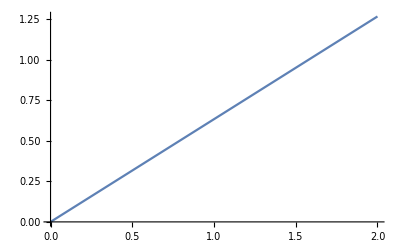

```mathematica
Plot[(2K 25)/(8Pi^2),{K,0,2}]
```

```mathematica
Plot[D[linsol[ss,5,1000,1,1.0,0.0],ss],{s,0,5}]
```

-Graphics-

```mathematica
0.002
```